## Ejercicio 3 - TP 01

Resolución de sistema lineal con RK4
Dudas:
1. ¿Está bien cómo aproximé y_j+1 con Euler?
2. ¿Está bien cómo lo encaré en Mathematica o hay una forma más sencilla de hacerlo?
3. ¿Por qué a le toma cada vez más tiempo hacer los cálculos con h pequeño?
4. En h = 1 no me lo ejecuta directamente
5. Por qué tarda tanto en estabilizar en el inciso b?

Inciso a

a = 1; b = 1;

h = {0.1,0.2,0.5,1.0}

Se observa que todas las soluciones numéricas convergen al mismo punto incluso para h grande. Aún más, modificando la condición inicial {x0,y0} se observó que también converge al mismo punto

Inciso b

a = 1; b = 3;

h = {0.1, 0.2, 0.5, 1}

(*Condición inicial dentro del ciclo y cerca del punto fijo*)

(*Condición inicial fuera del ciclo*)

```mathematica
f[x_,y_,a_,b_] :=a-(b+1) x + x^2 y ; (*función de EDO*)
g[x_,y_,a_,b_]:= b x - x^2 y; (*función de EDO*)
 
(*Defino las funciones que usaré en el método*)
(*k1x[x_,y_,a_,b_,h_]:=f[x,y,a,b];
k2x[x_,y_,a_,b_,h_]:=f[x+0.5h k1x[x,y,a,b], y + 0.5 h g[x,y,a,b],a,b];
k3x[x_,y_,a_,b_,h_]:=f[x+0.5 h k2x[x,y,a,b],y+0.5 h g[x,y,a,b],a,b];
k4x[x_,y_,a_,b_,h_]:=f[x+h k3x[x,y,a,b],y + h g[x,y,a,b],a,b];
*)
kx[x_,y_,a_,b_,h_] :={f[x,y,a,b],
						f[x+0.5h kx[x,y,a,b][[1]], y + 0.5 h g[x,y,a,b],a,b],
						f[x+0.5 h kx[x,y,a,b][[2]],y+0.5 h g[x,y,a,b],a,b],
						f[x+h kx[x,y,a,b][[3]],y + h g[x,y,a,b],a,b]}

ky[x_,y_,a_,b_,h_] :={g[x,y,a,b],
						g[x+0.5h f[x,y,a,b], y + 0.5 h ky[x,y,a,b][[1]],a,b],
						g[x+0.5 h f[x,y,a,b],y+0.5 h ky[x,y,a,b][[2]],a,b],
						g[x+h f[x,y,a,b],y + h ky[x,y,a,b][[3]],a,b]}

(*k1y[x_,y_,a_,b_,h_]:=g[x,y,a,b];
k2y[x_,y_,a_,b_,h_]:=g[x+0.5h f[x,y,a,b], y + 0.5 h k1y[x,y,a,b],a,b];
k3y[x_,y_,a_,b_,h_]:=g[x+0.5 h f[x,y,a,b],y+0.5 h k2y[x,y,a,b],a,b];
k4y[x_,y_,a_,b_,h_]:=g[x+h f[x,y,a,b],y + h k3y[x,y,a,b],a,b];*)

(*Defino las funciones que aplican el método. Cada una de ellas devuelve x_j+1 e y_j+1 respectivamente*)
RK4x[x_,y_,a_,b_,h_]:=x + (h/6) *(kx[x,y,a,b,h][[1]] + 2 kx[x,y,a,b,h][[2]] + 2kx[x,y,a,b,h][[3]] + kx[x,y,a,b,h])[[4]];
RK4y[x_,y_,a_,b_,h_]:=y + (h/6) *(ky[x,y,a,b,h][[1]] + 2 ky[x,y,a,b,h][[2]] + 2ky[x,y,a,b,h][[3]] + ky[x,y,a,b,h])[[4]];
kx[1,1,1,1,.1]
RK4x[1,1,1,1,0.1]
```

```mathematica
(*Defino las cosas devuelta pero más lindo:*)
RK4[x_,y_,f_,g_,h_]=Module[
kx1=f[x,y];
kx2 =f[x+0.5h kx1, y + 0.5 h g[x,y]];
kx3=f[x+0.5 h kx2,y+0.5 h g[x,y]];
kx4=f[x+h kx3,y + h g[x,y]];
ky1=g[x,y];
ky2=g[x+0.5h f[x,y], y + 0.5 h ky1];
ky3=g[x+0.5 h f[x,y],y+0.5 h ky2];
ky4=g[x+h f[x,y],y + h ky3];
,{x + (h/6) *(kx1+ 2 kx2 + 2kx3 + kx4), y + (h/6) *(ky1 + 2 ky2+ 2ky3+ ky4)}]
```

{0,0.0025,0.0025,0.01}

1.00033

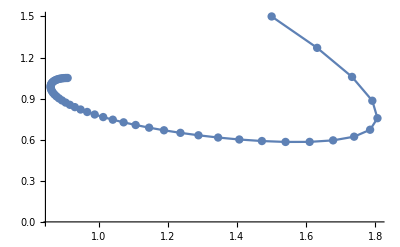

```mathematica
(*Condiciones iniciales*)
x0  =1.5;
y0 = 1.5;
a = 1;
b = 1;
(*Aplico el método*)
tmin = 0;
tmax = 5;
h = 0.1;
x = {x0};
y = {y0};
jmax = (tmax-tmin)/h; (*cant total de pasos*)
Do[
xnew = N[RK4x[x[[j]], y[[j]],a,b,h]]; (*aproximo*)
ynew = N[RK4y[x[[j]], y[[j]],a,b,h]]; (*aproximo*)
x = Append[x,xnew];
y = Append[y,ynew];
,{j,1,jmax-1}]
(*Grafico en el espacio de fases*)
ListPlot[Transpose[{x,y}],Joined->True, Mesh ->All,PlotRange->All]
```

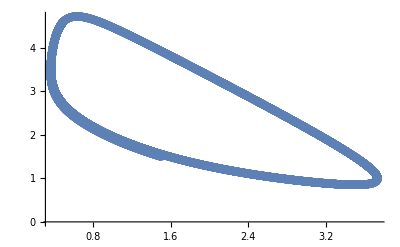

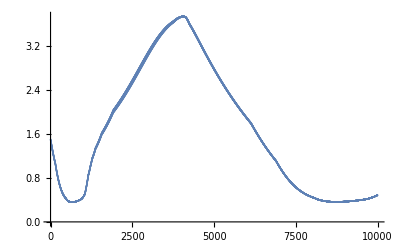

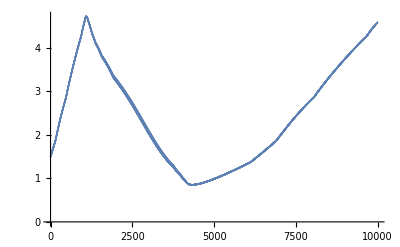

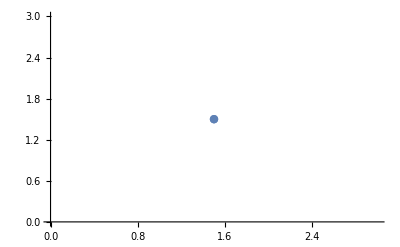

```mathematica
(*Paso adaptativo*)
(*Condiciones iniciales*)
x0  =1.5;
y0 = 1.5;
a = 1;
b = 3;
tol = 10^(-2);
(*Aplico el método*)
tmin = 0;
tmax = 50;
h = 0.1;
x = {x0};
y = {y0};
jmax = 10^4; (*cant total de pasos*)

saltos = 0;
Do[
j = j - saltos;
(*Print["j: ", j, " - h: ", h, "- saltos: ", saltos];*)
xnew1 = RK4x[x[[j]], y[[j]],a,b,h];
xnew2 = RK4x[x[[j]], y[[j]],a,b,h/2];
ynew1 =  RK4y[x[[j]], y[[j]],a,b,h];
ynew2 =  RK4y[x[[j]], y[[j]],a,b,h/2];

errorx = Abs[xnew2 - xnew1];
errory = Abs[ynew2 - ynew1];

caso1 = errorx>tol || errory > tol;
caso2 =(errorx> tol/2 && errorx<tol) || (errory> tol/2 && errory<tol);
caso3 = errorx<tol/2 && errory<tol/2;

If[caso1 == True,
h =h/1.5;
saltos = saltos + 1;
];
If[caso2 == True,
h =h;
x = Append[x,xnew2]; y = Append[y,ynew2];
];
If[caso3 == True,
h =1.5*h;
x = Append[x,xnew2]; y = Append[y,ynew2];
];
,{j,1,jmax-1}]
(*Grafico en el espacio de fases*)
ListPlot[Transpose[{x,y}],Joined->True, Mesh ->All,PlotRange->All]
ListPlot[x]
ListPlot[y]
```

### Inciso a

```mathematica
(*Aplico el método para distintos valores de h*)

tmin = 0;
tmax = 3;


a=1;b=1;
x0 = 2; y0 = 3;
h={0.1,0.2,0.5,1.0};
jmax = (tmax - tmin)/h;
g = {ListPlot[{a,b/a}]}
Do[
x = {x0};
y = {y0};
Do[
xnew = N[RK4x[x[[j]], y[[j]],a,b,h[[k]]]];
ynew = N[RK4y[x[[j]], y[[j]],a,b,h[[k]]]];
x = Append[x,xnew];
y = Append[y,ynew];
Print["Paso", j/jmax[[k]]];
,{j,1,jmax[[k]]-1}];
(*Grafico en el espacio de fases *)
g = Append[g,ListPlot[Transpose[{x,y}]]];,{k,1,4}];

Show[g]
```

Paso0.0333333

Paso0.0666667

Paso0.1

Paso0.133333

1

2

3

4

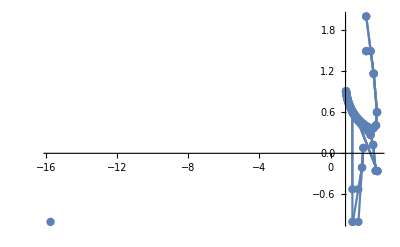

```mathematica
(*Aplico el método devuelta*)
(*Condiciones iniciales*)
x0  =2;
y0 = 2;
a = 1;
b = 1;

(*Aplico el método*)
tmin = 0;
tmax = 3;
h = {0.1,0.2,0.5,1.0};
x = {x0};
y = {y0};
jmax = (tmax-tmin)/h; (*cant total de pasos*)


k = 1; Print[k]
Do[
xnew = N[RK4x[x[[j]], y[[j]],a,b,h[[k]]]]; (*aproximo*)
ynew = N[RK4y[x[[j]], y[[j]],a,b,h[[k]]]]; (*aproximo*)
x = Append[x,xnew];
y = Append[y,ynew];
,{j,1,jmax[[k]]-1}]
(*Grafico en el espacio de fases*)
g1= ListLinePlot[Transpose[{x,y}],Joined->True, Mesh ->All];

k = 2; Print[k]
Do[
xnew = N[RK4x[x[[j]], y[[j]],a,b,h[[k]]]]; (*aproximo*)
ynew = N[RK4y[x[[j]], y[[j]],a,b,h[[k]]]]; (*aproximo*)
x = Append[x,xnew];
y = Append[y,ynew];
,{j,1,jmax[[k]]-1}]
(*Grafico en el espacio de fases*)
g2= ListLinePlot[Transpose[{x,y}],Joined->True, Mesh ->All];

k = 3; Print[k]
Do[
xnew = N[RK4x[x[[j]], y[[j]],a,b,h[[k]]]]; (*aproximo*)
ynew = N[RK4y[x[[j]], y[[j]],a,b,h[[k]]]]; (*aproximo*)
x = Append[x,xnew];
y = Append[y,ynew];
,{j,1,jmax[[k]]-1}]
(*Grafico en el espacio de fases*)
g3= ListLinePlot[Transpose[{x,y}],Joined->True, Mesh ->All];

k = 4; Print[k]
Do[
xnew = N[RK4x[x[[j]], y[[j]],a,b,h[[k]]]]; (*aproximo*)
ynew = N[RK4y[x[[j]], y[[j]],a,b,h[[k]]]]; (*aproximo*)
x = Append[x,xnew];
y = Append[y,ynew];
,{j,1,jmax[[k]]-1}]
(*Grafico en el espacio de fases*)
g4= ListLinePlot[Transpose[{x,y}],Joined->True, Mesh ->All];
Show[{g1,g2,g3,g4},PlotRange->All]
```

```mathematica
f[x_,y_]:=x^2 + y
g[x_,y_]:=Sin[f[x,y]]
f[1,2]
g[1,1]
N[g[1,1]]
(*POR QUÉ NO EVALÚA??*)
```

```mathematica
N[Sin[4]]
```

-0.756802

```mathematica
f[x_,y_,a_,b_] :=a-(b+1) x + x^2 y ;
f[1,1,1,1]
k1x[x_,y_,a_,b_,h_]:=f[x,y,a,b];
k1x[1,1,1,1,1]
N[k1x[1,1,1,1,1]]
N[k1x[1,1,1,1,1],10] (*POR QUÉ NO EVALÚA?? LE FALTAN ARGUMENTOS!*)
```

0

0

0.

0